```mathematica
d2=Monitor[Table[
x/.NSolve[CyclePoly[k]==0,x]
,{k,1,300}],k]
```

{{0.},298,{-1.41075,-1.39151,-1.3686,-1.36379,-1.35572,-1.33437,-1.32615,-1.3218,-1.31915,-1.31241,-1.30801,-1.28199,-1.27324,-1.26814,-1.26262,-1.22474,-1.20392,-1.19184,-1.18065,-1.16556,-1.16317,-1.13789,-1.10094,-1.09023,-1.08759,-1.07606,-1.06479,-1.04529,-1.02879,-1.01628,-0.963764,-0.945118,-0.917309,-0.905206,-0.88791,-0.854698,-0.840314,-0.816761,-0.800272,-0.796509,-0.786297,-0.769674,-0.761093,-0.730197,-0.705483,-0.699966,-0.699863,-0.66607,-0.659426,-0.636745,-0.630573,-0.599915,-0.599693,-0.58914,-0.566654,-0.563873,-0.53249,-0.52228,-0.500687,-0.490797,-0.468645,-0.467912,-0.463297,-0.460536,-0.438588,-0.434705,-0.423413,-0.414119,-0.400857,-0.387649,-0.378049,-0.37709,-0.354888,-0.349821,-0.33762,-0.328998,-0.327152,-0.310518,-0.309289,-0.30177,-0.29025,-0.281423,-0.272759,-0.2689,-0.255952,-0.24685,-0.237248,-0.223776,-0.215283,-0.200781,-0.196011,-0.192065,-0.190916,-0.180918,-0.163671,-0.158088,-0.145437,-0.142195,-0.137786,-0.12751,-0.122214,-0.10912,-0.103864,-0.102498,-0.0953212,-0.0948138,-0.0901988,-0.0886968,-0.0827602,-0.0733111,-0.0727985,-0.0709499,-0.066043,-0.0655132,-0.0652992,-0.0581791,-0.0549248,-0.051231,-0.0446235,-0.0435341,-0.0375674,-0.0330994,-0.0316561,-0.0313396,-0.0276327,-0.0223169,-0.0157186,46,0.124032,0.125155,0.125792,0.126055,0.127705,0.128139,0.13519,0.144089,0.149034,0.161323,0.168245,0.178737,0.185516,0.19039,0.190509,0.19476,0.218496,0.223562,0.225271,0.22585,0.237078,0.258259,0.262518,0.281643,0.290166,0.312103,0.312877,0.356553,0.376674,0.387663,0.404006,0.441915,0.474327,0.495798,0.499963,0.514398,0.519836,0.523752,0.524894,0.557739,0.560995,0.571166,0.589695,0.59241,0.598751,0.617715,0.632076,0.669441,0.674567,0.687145,0.711266,0.730881,0.790479,0.822147,0.83339,0.910905,0.92081,0.931013,0.941915,0.989474,0.992981,1.00369,1.03326,1.09792,1.12405,1.18569,1.24725,1.43628,1.487,1.55638,1.59654,1.66055,1.68608,1.7621,1.80445,2.12484,2.14816,2.16014,2.16625,2.17221,2.48401,2.52474,2.55469,2.55713,2.85064,2.97455,3.12443,3.22259,3.48627,3.58902,3.666,3.80191,3.81653,3.87404,4.16815,4.19728,4.21661,4.3517,4.3547,5.10319,5.31694,5.31727,5.34633,5.68885,5.83342,5.99347,6.17205,6.39285,6.71724,7.30081,7.41445,7.6684,7.82064,8.56605,9.50915,9.85496,10.9402,11.4179,11.7891,12.5622,13.1635,13.252,15.0175,15.46,15.833,16.187,16.4936}}
 |  |  |  |

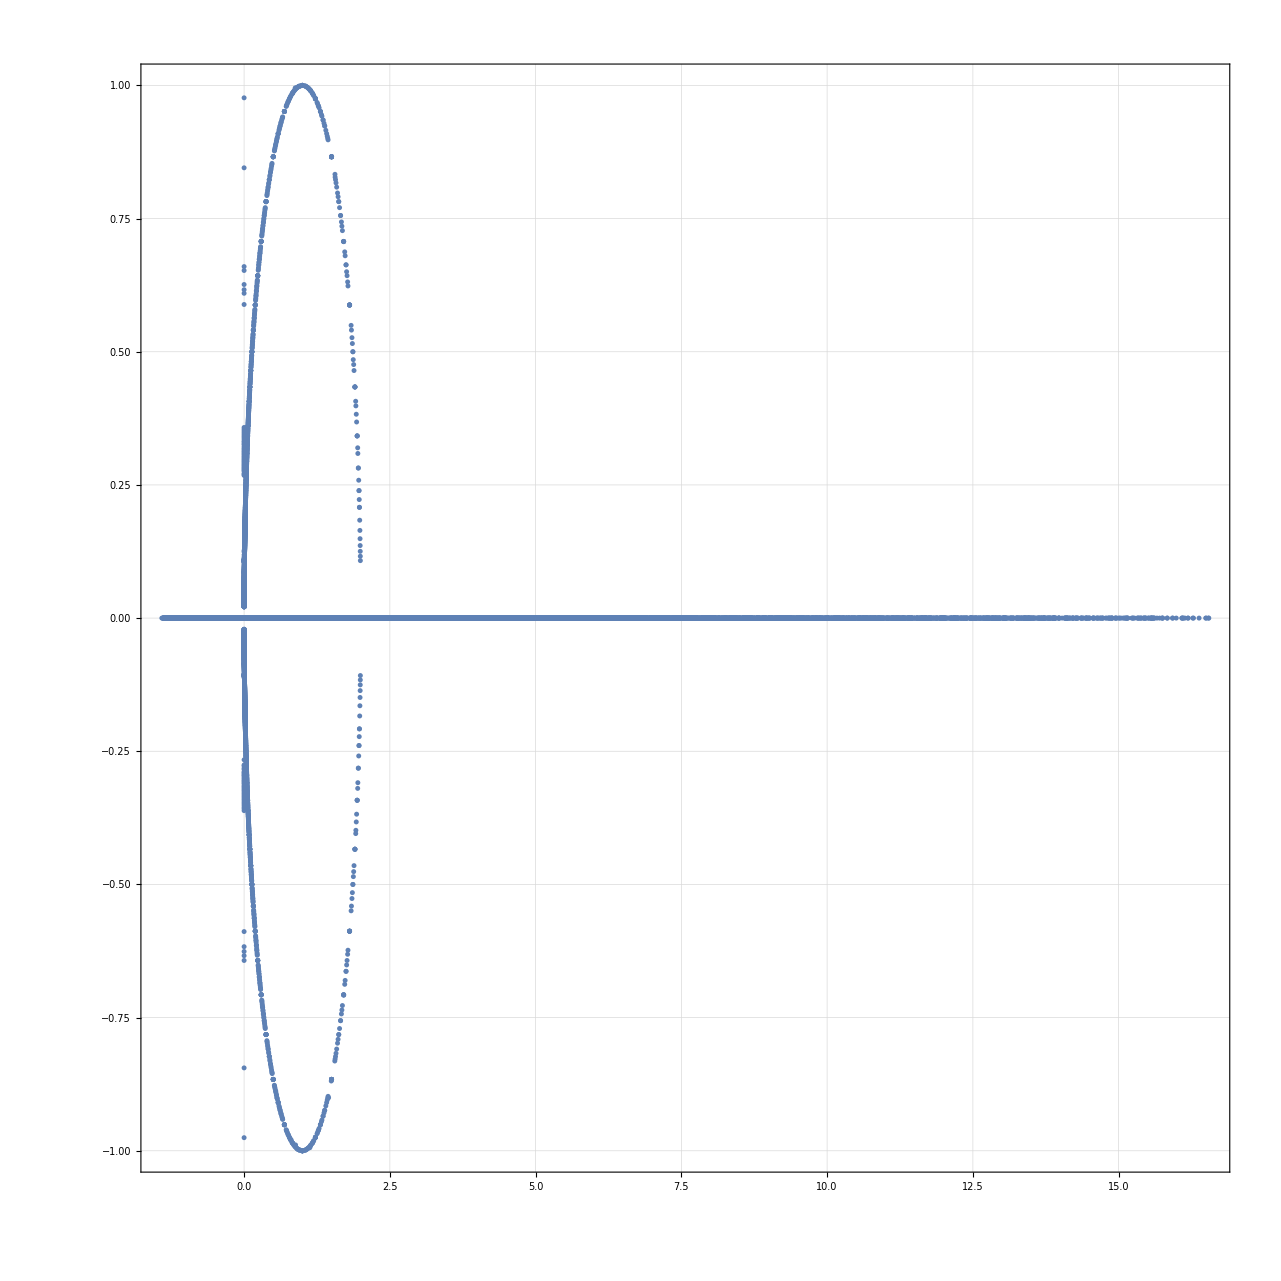

```mathematica
ListPlot[Map[{Re[#],Im[#]}&,Flatten[d2]], PlotRange->All,GridLines->Automatic,Frame->True, AspectRatio->1]
```

```mathematica
d3=Monitor[Table[
With[{g=DiamondGraph[k]},
x/.NSolve[ChromaticPolynomial[g,x]==0,x]
]
,{k,1,25}],k]
```

{{0.,1.,1.},{0.,1.,2.,2.},{0.+0. ⅈ,1.,2.,2.5-0.866025 ⅈ,2.5+0.866025 ⅈ},{0.+0. ⅈ,1.,2.,2.43016,2.78492-1.30714 ⅈ,2.78492+1.30714 ⅈ},{0.+0. ⅈ,1.,2.,2.44796-0.242275 ⅈ,2.44796+0.242275 ⅈ,3.05204-1.65794 ⅈ,3.05204+1.65794 ⅈ},{0.+0. ⅈ,1.,2.,2.45958-0.421728 ⅈ,2.45958+0.421728 ⅈ,2.4614,3.30972-1.96346 ⅈ,3.30972+1.96346 ⅈ},{0.+0. ⅈ,1.,2.,2.46776-0.147114 ⅈ,2.46776+0.147114 ⅈ,2.4715-0.579225 ⅈ,2.4715+0.579225 ⅈ,3.56073-2.24051 ⅈ,3.56073+2.24051 ⅈ},{0.+0. ⅈ,1.,2.,2.47193-0.262907 ⅈ,2.47193+0.262907 ⅈ,2.47331,2.48491-0.725845 ⅈ,2.48491+0.725845 ⅈ,3.8065-2.49747 ⅈ,3.8065+2.49747 ⅈ},{0.+0. ⅈ,1.,2.,2.47548-0.363889 ⅈ,2.47548+0.363889 ⅈ,2.4766-0.106388 ⅈ,2.4766+0.106388 ⅈ,2.5-0.866025 ⅈ,2.5+0.866025 ⅈ,4.04792-2.73925 ⅈ,4.04792+2.73925 ⅈ},{0.+0. ⅈ,1.,2.,2.4789-0.193882 ⅈ,2.4789+0.193882 ⅈ,2.47896-0.456499 ⅈ,2.47896+0.456499 ⅈ,2.4796,2.5167-1.00194 ⅈ,2.5167+1.00194 ⅈ,4.28564-2.96901 ⅈ,4.28564+2.96901 ⅈ},{0.+0. ⅈ,1.,2.,2.48078-0.270825 ⅈ,2.48078+0.270825 ⅈ,2.48161-0.0834871 ⅈ,2.48161+0.0834871 ⅈ,2.4826-0.543839 ⅈ,2.4826+0.543839 ⅈ,2.53489-1.1348 ⅈ,2.53489+1.1348 ⅈ,4.52011-3.18892 ⅈ,4.52011+3.18892 ⅈ},{0.+0. ⅈ,1.,2.,2.48248-0.341178 ⅈ,2.48248+0.341178 ⅈ,2.4831-0.154317 ⅈ,2.4831+0.154317 ⅈ,2.48351,2.4865-0.627609 ⅈ,2.4865+0.627609 ⅈ,2.55445-1.26534 ⅈ,2.55445+1.26534 ⅈ,4.75172-3.40058 ⅈ,4.75172+3.40058 ⅈ},{0.+0. ⅈ,1.,2.,2.48413-0.407093 ⅈ,2.48413+0.407093 ⅈ,2.48432-0.217299 ⅈ,2.48432+0.217299 ⅈ,2.48485-0.0687658 ⅈ,2.48485+0.0687658 ⅈ,2.4907-0.70883 ⅈ,2.4907+0.70883 ⅈ,2.57526-1.39405 ⅈ,2.57526+1.39405 ⅈ,4.98075-3.60515 ⅈ,4.98075+3.60515 ⅈ},{0.+0. ⅈ,1.,2.,2.48537-0.275015 ⅈ,2.48537+0.275015 ⅈ,2.48581-0.46986 ⅈ,2.48581+0.46986 ⅈ,2.48597-0.127891 ⅈ,2.48597+0.127891 ⅈ,2.48639,2.4952-0.788156 ⅈ,2.4952+0.788156 ⅈ,2.5972-1.52125 ⅈ,2.5972+1.52125 ⅈ,5.20745-3.80357 ⅈ,5.20745+3.80357 ⅈ},{0.+0. ⅈ,1.,2.,2.47633,2.48641+0.328932 ⅈ,2.48646-0.328852 ⅈ,2.48663,2.48756+0.530314 ⅈ,2.48756-0.530295 ⅈ,2.4883,2.49361,2.5+0.866026 ⅈ,2.5-0.866025 ⅈ,2.62018+1.64718 ⅈ,2.62018-1.64718 ⅈ,5.43201-3.99657 ⅈ,5.43201+3.99657 ⅈ},{0.+0. ⅈ,1.,1.99992,2.41997,2.42823,2.47823,2.48282,2.48931-0.588889 ⅈ,2.48944,2.48965+0.588846 ⅈ,2.5051+0.942746 ⅈ,2.5051-0.942746 ⅈ,2.51153,2.54285,2.64412+1.77202 ⅈ,2.64412-1.77202 ⅈ,5.65462+4.18474 ⅈ,5.65462-4.18474 ⅈ},{0.+0. ⅈ,1.,1.99979,2.3528,2.35816,2.43822,2.43978,2.47618,2.49105-0.64644 ⅈ,2.4911+0.646367 ⅈ,2.51046-1.01854 ⅈ,2.51049+1.01854 ⅈ,2.52894,2.53408,2.64342,2.66894+1.8959 ⅈ,2.66894-1.8959 ⅈ,5.87541-4.36858 ⅈ,5.87541+4.36858 ⅈ},{0.+0. ⅈ,1.,2.00029,2.22106,2.25724,2.37214,2.38223,2.45531,2.49318-0.701996 ⅈ,2.4936+0.70162 ⅈ,2.50361,2.51616+1.09358 ⅈ,2.51617-1.09358 ⅈ,2.65532,2.69458+2.01893 ⅈ,2.69458-2.01893 ⅈ,2.71244,2.7236,6.09452-4.54849 ⅈ,6.09452+4.54849 ⅈ},{0.+0. ⅈ,1.,1.99462,2.1421,2.20161,2.27451,2.31126,2.35827,2.47449,2.4937+0.763322 ⅈ,2.5111,2.5221-1.16798 ⅈ,2.5221+1.16797 ⅈ,2.61282,2.72098+2.14118 ⅈ,2.72098-2.14118 ⅈ,2.76169,2.792,2.80551,6.31205-4.72481 ⅈ,6.31205+4.72481 ⅈ},{0.+0. ⅈ,1.,2.0128,2.02195,2.09244,2.16303,2.21525,2.29808,2.40573,2.43181,2.50196,2.51778,2.52829+1.24185 ⅈ,2.52835-1.24192 ⅈ,2.73853,2.74809+2.26274 ⅈ,2.74809-2.26274 ⅈ,2.81892,2.88699,2.9373,6.5281+4.89786 ⅈ,6.5281-4.89786 ⅈ},{0.+0. ⅈ,1.,1.93556,2.03865,2.04408,2.10812,2.15516,2.21598,2.30995,2.42605,2.44639,2.53468-1.31524 ⅈ,2.53472+1.31521 ⅈ,2.54577,2.76584,2.77586+2.38365 ⅈ,2.77586-2.38365 ⅈ,2.7903,2.87942,2.99032,3.00566,6.74277-5.06788 ⅈ,6.74277+5.06788 ⅈ},{0.+0. ⅈ,1.,1.93442,1.94237,1.98115,2.0332,2.13924,2.14784,2.24088,2.24613,2.46637,2.47836,2.54128+1.3884 ⅈ,2.54138-1.3882 ⅈ,2.68868,2.80426+2.50397 ⅈ,2.80426-2.50397 ⅈ,2.82645,2.99326,2.99472,3.11454,3.14331,6.95613+5.2351 ⅈ,6.95613-5.2351 ⅈ},{0.+0. ⅈ,1.,1.85563,1.88479,1.91942,1.92504,1.99224,2.06269,2.10265,2.15279,2.27001,2.38344,2.47702,2.54827+1.46109 ⅈ,2.54834-1.46082 ⅈ,2.63328,2.80893,2.83325+2.62374 ⅈ,2.83325-2.62374 ⅈ,2.93168,3.21254,3.24805,3.27695,7.16825+5.39972 ⅈ,7.16825-5.39972 ⅈ},{0.+0. ⅈ,1.,1.81099,1.86273,1.88187,1.89505,1.95325,1.99771,2.02956,2.16961,2.21738,2.41185,2.4193,2.55518+1.53316 ⅈ,2.55532-1.53326 ⅈ,2.72087,2.77361,2.86279+2.74298 ⅈ,2.86279-2.74298 ⅈ,3.11729,3.20719,3.30984,3.317,3.36176,7.3792+5.56191 ⅈ,7.3792-5.56191 ⅈ},{0.+0. ⅈ,1.,1.75719,1.81561,1.82017,1.84456,1.89898,1.91576,1.97659,2.06009,2.17588,2.2613,2.41465,2.42809,2.55968-1.60751 ⅈ,2.56322+1.6076 ⅈ,2.81404,2.89285+2.86174 ⅈ,2.89285-2.86174 ⅈ,2.95355,3.05818,3.13032,3.43097,3.52199,3.52481,7.58902+5.72182 ⅈ,7.58902-5.72182 ⅈ}}

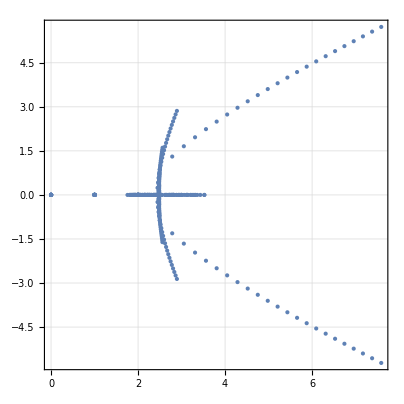

```mathematica
ListPlot[Map[{Re[#],Im[#]}&,Flatten[d3]], PlotRange->All,GridLines->Automatic,Frame->True, AspectRatio->1]
```

```mathematica
Monitor[Table[
Solve[CyclePoly[k]==0,x]
,{k,1,500,100}],k]
```

{{{x→0}},3,{{x→0},{x→1},397,{x→Root[1]},{x→Root[1-80 #1+7960 #1^2-461360 #1^3+19569980 #1^4-653188016 #1^5+17837170520 #1^6-409922095440 #1^7+8105710409290 #1^8-140374298249120 #1^9+2159626353131312 #1^10-29859551133245600 #1^11+374555204463343800 #1^12-4296235813995017600 #1^13+45358923466349382400 #1^14-443270581524198245440 #1^15+195+46026828991565696400 #1^146-4383507523006256800 #1^147+385037822966765800 #1^148-31009757554370400 #1^149+2274048887320496 #1^150-150599264060960 #1^151+8917061687820 #1^152-466251591520 #1^153+21193254160 #1^154-820384032 #1^155+26294360 #1^156-669920 #1^157+12720 #1^158-160 #1^159+#1^160&,160]}}}
 |  |  |  |